```mathematica
SetDirectory[".../Data"]; (*Set this to your folder where the Data folder is*)
```

```mathematica
SetOptions[ListPlot,BaseStyle->{FontFamily->"Times",FontSize->20}];
```

```mathematica
c1=-28;
c2=5.474;
c3=0.01;
c4=0.278;
c5=0.0055;
c6=0.165;
```

```mathematica
s1=c1;
s2=c2(2 c4 - c6)/(2 c4 + c6); 
s3=c3 + 2 c2 c6 /(2 c4 + c6);
s4 = c4 ((2 c4 - c6) ^2) /((2 c4 + c6)^2);
s5=c5 + 2 c6^3/(2 c4 + c6)^2;
s6=c6(2c4 - c6)^2 /(2 c4 + c6)^2;
```

```mathematica
pc[a_,x_]:=c1 + c2 a + c3 x - c4 a^2+c5 x^2 + c6 a x
```

```mathematica
ps[a_,x_]:=s1 + s2 a + s3 x - s4 a^2+s5 x^2 - s6 a x
```

```mathematica
pcloss[a_,x_,loss_]:=Module[{pi},
pi=pc[a,x];
If[pi<0,Return[loss*pi],Return[pi]]
]
```

```mathematica
psloss[a_,x_,loss_]:=Module[{pi},
pi=ps[a,x];
If[pi<0,Return[loss*pi],Return[pi]]
]
```

```mathematica
Table[pc[a,0],{a,0,28,2}]
```

{-28.,-18.164,-10.552,-5.164,-2.,-1.06,-2.344,-5.852,-11.584,-19.54,-29.72,-42.124,-56.752,-73.604,-92.68}

```mathematica
Table[ps[a,0],{a,0,28,2}]
```

{-28.,-22.3899,-17.4339,-13.1319,-9.48398,-6.49012,-4.15033,-2.46459,-1.43292,-1.0553,-1.33175,-2.26226,-3.84682,-6.08545,-8.97814}

## data

```mathematica
sub={2,28,10,2,4,18,28,14,2,16,14,28,10,25,4,18,10,14,28,28,18,28,28,4,22,10,12,15.2,2,2,2,18,5,10,28,16,28,2,0,22,10,8,28,0,26,22,19,0,12,28,12,5,16,10.1,28,5.4,10,16,1,3,2,0,12,22,18,28,3,10,4,28,28,5,2,28,14,22,20,0,18,4,7,1,24,0.5,9,12,18,22,18,20,17.5,0,15,26,13,28,18,16,14,18,10,28,10,10,18,26,28,28,28,28,28,9}
```

{2,28,10,2,4,18,28,14,2,16,14,28,10,25,4,18,10,14,28,28,18,28,28,4,22,10,12,15.2,2,2,2,18,5,10,28,16,28,2,0,22,10,8,28,0,26,22,19,0,12,28,12,5,16,10.1,28,5.4,10,16,1,3,2,0,12,22,18,28,3,10,4,28,28,5,2,28,14,22,20,0,18,4,7,1,24,0.5,9,12,18,22,18,20,17.5,0,15,26,13,28,18,16,14,18,10,28,10,10,18,26,28,28,28,28,28,9}

```mathematica
comp={26,14,18,2,18,15,2,24,8,12,28,15,18,18,2,0,20,0,20,18,18,2,8,2,26,0,18,4,3,10,14.2,10,24,3,16,28,10,18,26,28,22,4,14,16,10,8,12,18,3,14,2,20,14,16.4,18,18,10,2,12,28,20,10,5.5,10,28,18,18,28,0.4,2,4,11.5,10,22,14,18,25.7,28,18,28,18,15,18,8,18,28,18,14,18,12,8,26.9,8,2,26,26,22,26,28,16,14,14}
```

{26,14,18,2,18,15,2,24,8,12,28,15,18,18,2,0,20,0,20,18,18,2,8,2,26,0,18,4,3,10,14.2,10,24,3,16,28,10,18,26,28,22,4,14,16,10,8,12,18,3,14,2,20,14,16.4,18,18,10,2,12,28,20,10,5.5,10,28,18,18,28,0.4,2,4,11.5,10,22,14,18,25.7,28,18,28,18,15,18,8,18,28,18,14,18,12,8,26.9,8,2,26,26,22,26,28,16,14,14}

## Reinforcement learning

```mathematica
choice[att_,lambda_,step_]:=Module[{pdf,sum,cdf,rand,i,cum,choice},
(*att=Table[Mean[Table[pcloss[a,x,loss],{x,0,28,step2}]],{a,0,28,step1}];*)
(*Print[att]*)
pdf=Exp[lambda*att];
sum=Plus@@pdf;
cdf=pdf/sum;
rand=Random[];
i=1;
cum=cdf[[i]];
While[rand>cum,
i++;
cum+=cdf[[i]];
];
choice=step*(i-1);
Return[choice];
]
```

```mathematica
attEvolution[att_,weight_,choice_,step_,pay_]:=Module[{new,part,att1},
part=IntegerPart[choice/step+1];
(*Print[part];*)
new=weight*att[[part]]+(1.0-weight)*pay;
(*Print[new];*)
att1=ReplacePart[att,part->new];
(*Print[att1];*)
Return[att1]
]
```

```mathematica
DegreeCorp[dat_]:=Module[{obs,rest,i,temp},
obs=Length[dat];
(*Print[obs];*)
rest={};
Do[
temp=Table[(Mean[dat[[{i,i+1},t]]]-14.0)/(25.5-14.0),{t,1,30}];
(*Print[temp];*)
AppendTo[rest,temp];
,{i,1,obs,2}];
Return[rest];
];
```

```mathematica
AverageDegreeCorp[dat_]:=Module[{obs,rest,i,temp,ave},
obs=Length[dat];
(*Print[obs];*)
rest={};
Do[
temp=Table[(Mean[dat[[{i,i+1},t]]]-14.0)/(25.5-14.0),{t,1,30}];
(*Print[temp];*)
ave=Mean[temp];
AppendTo[rest,ave];
,{i,1,obs,2}];
Return[rest];
];
```

```mathematica
RLC2Uniform[lambda_,step_,loss_,weight_,obs_]:=Module[{c1,c2,p1,p2,result,res1,res2,x,y,att1,att2,mp},
result={};
Do[
res1={};
res2={};
mp=Mean[Flatten[Table[Table[pcloss[a,x,loss],{x,0,28,step}],{a,0,28,step}]]];
att1=Table[mp,{i,0,28,step}];
att2=Table[mp,{i,0,28,step}];
c1=choice[att1,lambda,step];
c2=choice[att2,lambda,step];
p1=pcloss[c1,c2,loss];
p2=pcloss[c2,c1,loss];
AppendTo[res1,c1];
AppendTo[res2,c2];
Do[
att1=attEvolution[att1,weight,c1,step,p1];
att2=attEvolution[att2,weight,c2,step,p2];
c1=choice[att1,lambda,step];
c2=choice[att2,lambda,step];
p1=pcloss[c1,c2,loss];
p2=pcloss[c2,c1,loss];
AppendTo[res1,c1];
AppendTo[res2,c2];
,{29}];
AppendTo[result,res1];
AppendTo[result,res2],
{i,1,obs}];
Return[result]

]
```

```mathematica
RLS2Uniform[lambda_,step_,loss_,weight_,obs_]:=Module[{c1,c2,p1,p2,result,res1,res2,x,y,att1,att2,mp},
result={};
Do[
res1={};
res2={};
mp=Mean[Flatten[Table[Table[psloss[a,x,loss],{x,0,28,step}],{a,0,28,step}]]];
att1=Table[mp,{i,0,28,step}];
att2=Table[mp,{i,0,28,step}];
c1=choice[att1,lambda,step];
c2=choice[att2,lambda,step];
p1=psloss[c1,c2,loss];
p2=psloss[c2,c1,loss];
AppendTo[res1,c1];
AppendTo[res2,c2];
Do[
att1=attEvolution[att1,weight,c1,step,p1];
att2=attEvolution[att2,weight,c2,step,p2];
c1=choice[att1,lambda,step];
c2=choice[att2,lambda,step];
p1=psloss[c1,c2,loss];
p2=psloss[c2,c1,loss];
AppendTo[res1,c1];
AppendTo[res2,c2];
,{29}];
AppendTo[result,res1];
AppendTo[result,res2],
{i,1,obs}];
Return[result]
]
```

```mathematica
GenGridData[lambda_,step_,loss_,weight_,obs_,comp_,func_,init_]:=Module[{dat},
If[comp==1(*complementarity*),
If[func==3(*mean init attraction*)&&init==0(*model driven initial choice*),
dat=AverageDegreeCorp[RLC2Uniform[lambda,step,loss,weight,obs]];
];
];
If[comp==0(*substitute*),
If[func==3(*mean init attraction*)&&init==0(*model driven initial choice*),
dat=AverageDegreeCorp[RLS2Uniform[lambda,step,loss,weight,obs]];
];
];
Return[Flatten[{lambda, step,loss, weight,comp,func,init,Mean[dat],StandardDeviation[dat]}]]];
```

## Produce UniformAll

```mathematica
SimDatCompUniformModel2={};
```

```mathematica
Do[Do[
AppendTo[SimDatCompUniformModel2,
GenGridData[l,1.0,1.0,w,100,1,3,0]],{l,0.1,1.5,0.2}],{w,0.05,0.95,0.05}]
```

```mathematica
Export["simdatcompuniformmodel2.csv",SimDatCompUniformModel2,"CSV"]
```

simdatcompuniformmodel2.csv

```mathematica
SimDatSubUniformModel2={};
```

```mathematica
Do[Do[
AppendTo[SimDatSubUniformModel2,
GenGridData[l,1.0,1.0,w,100,0,3,0]],{l,0.1,1.5,0.2}],{w,0.05,0.95,0.05}]
```

```mathematica
Export["simdatsubuniformmodel2.csv",SimDatSubUniformModel2,"CSV"]
```

simdatsubuniformmodel2.csv

```mathematica
l15difuniform2=Table[{y,Select[SimDatCompUniformModel2,(#[[1]]==1.5&&#[[4]]==y)&][[1,8]]-Select[SimDatSubUniformModel2,(#[[1]]==1.5&&#[[4]]==y)&][[1,8]]},{y,0.05,0.95,0.05}]
```

{{0.05,-0.20471},{0.1,-0.245391},{0.15,-0.162145},{0.2,-0.137},{0.25,-0.185304},{0.3,-0.189116},{0.35,-0.137826},{0.4,-0.157841},{0.45,-0.157449},{0.5,-0.239681},{0.55,-0.163739},{0.6,-0.251072},{0.65,-0.158362},{0.7,-0.157754},{0.75,-0.0805652},{0.8,0.0125072},{0.85,0.0206957},{0.9,0.0116957},{0.95,0.102072}}

```mathematica
l09difuniform2=Table[{y,Select[SimDatCompUniformModel2,(#[[1]]==0.9&&#[[4]]==y)&][[1,8]]-Select[SimDatSubUniformModel2,(#[[1]]==0.9&&#[[4]]==y)&][[1,8]]},{y,0.05,0.95,0.05}]
```

{{0.05,-0.164246},{0.1,-0.105812},{0.15,-0.165609},{0.2,-0.247536},{0.25,-0.103043},{0.3,-0.201928},{0.35,-0.14187},{0.4,-0.143841},{0.45,-0.146855},{0.5,-0.216188},{0.55,-0.0337971},{0.6,-0.00765217},{0.65,-0.000304348},{0.7,-0.0326232},{0.75,0.0172609},{0.8,0.00926087},{0.85,0.0702754},{0.9,0.059942},{0.95,0.0712464}}

```mathematica
l05difuniform2=Table[{y,Select[SimDatCompUniformModel2,(#[[1]]==0.5&&#[[4]]==y)&][[1,8]]-Select[SimDatSubUniformModel2,(#[[1]]==0.5&&#[[4]]==y)&][[1,8]]},{y,0.05,0.95,0.05}]
```

{{0.05,-0.0232754},{0.1,-0.108652},{0.15,-0.0547681},{0.2,-0.0177971},{0.25,-0.0648261},{0.3,0.0295507},{0.35,0.00417391},{0.4,0.009},{0.45,0.077},{0.5,0.0623913},{0.55,0.0231884},{0.6,0.135652},{0.65,0.144377},{0.7,0.094942},{0.75,0.0591884},{0.8,0.127754},{0.85,0.144812},{0.9,0.0594348},{0.95,0.0685797}}

```mathematica
l01difuniform2=Table[{y,Select[SimDatCompUniformModel2,(#[[1]]==0.1&&#[[4]]==y)&][[1,8]]-Select[SimDatSubUniformModel2,(#[[1]]==0.1&&#[[4]]==y)&][[1,8]]},{y,0.05,0.95,0.05}]
```

{{0.05,0.0452754},{0.1,0.039029},{0.15,0.0256957},{0.2,0.0771014},{0.25,0.0660435},{0.3,0.022058},{0.35,0.031942},{0.4,0.0512754},{0.45,0.0368841},{0.5,0.0767536},{0.55,0.0575942},{0.6,0.0381014},{0.65,0.0382899},{0.7,0.045913},{0.75,0.0465507},{0.8,0.0355797},{0.85,0.0147101},{0.9,0.0365362},{0.95,0.0145797}}

```mathematica
Export["l01difuniform2.csv",l01difuniform2,"CSV"];
Export["l05difuniform2.csv",l05difuniform2,"CSV"];
Export["l09difuniform2.csv",l09difuniform2,"CSV"];
Export["l1difuniform2.csv",l15difuniform2,"CSV"];

Jo1=Join[l01difuniform2,l05difuniform2,2]
Jo2=Join[l09difuniform2,l15difuniform2,2]
UniformAll=Join[Jo1,Jo2,2]
(*Removing underdash below will replace the default file in the package*)
Export["UniformAll_.csv",UniformAll,"CSV"];
```

```mathematica
(* Figure 6, this is reproduced in R with RLSimulation.R file using UniformAll.csv produced above *)
```

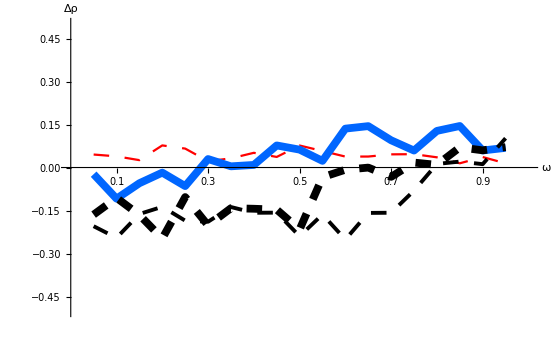

```mathematica
ListPlot[{l01difuniform2,l05difuniform2,l09difuniform2,l15difuniform2},Joined->True,PlotRange->{{0,1},{-0.5,0.5}},AxesLabel->{"ω","Δρ"},PlotStyle->{{Hue[0],Dashing[{0.02,0.02}]},{Hue[0.6],Thickness[0.01]},{GrayLevel[0],Thickness[0.01],Dashing[{0.02,0.02}]},{GrayLevel[0],Thickness[0.005],Dashing[{0.02,0.02}]}},Ticks->{{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0},Automatic}]
```

```mathematica
Export["difUniformModel.pdf",%,"PDF"];
```